```mathematica
removeAll:=Remove[Evaluate[$Context<>"*"]];

removeAll

(* Считаем для сервера RH1288 *)
Protect[ℛrh1288,ℛrh2288,ℛos5500head];Remove[Evaluate[$Context<>"*"]];Unprotect[ℛrh1288,ℛrh2288,ℛos5500head]

Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"RAID","3 - C"->"CPU","4 - D"->"RAM","5 - E"->"FAN","6 - F"->"HDD",
"7 - G"->"PS (Power Supply)","8 - H"->"NET","9 - I"->"FC (Fiber Channel)"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{{{Subscript[x, 1],ExponentialDistribution[4035×10^-9]}, {Subscript[x, 2],ExponentialDistribution[559×10^-9]}},Array[{Subscript[c, #],ExponentialDistribution[40×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[50×10^-9]}&,10], Array[{Subscript[e, #],ExponentialDistribution[582×10^-9]}&,4],Array[{Subscript[f, #],ExponentialDistribution[3425×10^-9]}&,2],Array[{Subscript[g, #],ExponentialDistribution[2000×10^-9]}&,2],Array[{Subscript[h, #],ExponentialDistribution[362×10^-9]}&,2],Array[{Subscript[i, #],ExponentialDistribution[362×10^-9]}&,2]} ,1];
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (* CPU *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (* RAM *)
Subscript[x, 5]=BooleanCountingFunction[{3,4},4]@@Array[Subscript[e, #]&,4] //BooleanConvert ;(* FAN *)
Subscript[x, 6]=Or @@Array[Subscript[f, #]&,2]; (* HDD *)
Subscript[x, 7]=Or @@Array[Subscript[g, #]&,2]; (* PS *)
Subscript[x, 8]=Or @@Array[Subscript[h, #]&,2]; (* NET *)
Subscript[x, 9]=Or @@Array[Subscript[i, #]&,2]; (* FC *)
bexpr=And @@Array[Subscript[x, #]&,9];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛrh1288=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛrh1288,t]
Plot[SurvivalFunction[ℛrh1288,t]//Evaluate,{t,0,400000},PlotRange->All]
(* mttf=NExpectation[t,t\[Distributed]ℛrh1288] (* идентично mttf=Mean[ℛrh1288] *) *)
mttf = Mean[ℛrh1288] //N
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)
```

```mathematica
(* Считаем для сервера RH2288 *)
Protect[ℛrh1288,ℛrh2288,ℛos5500head];Remove[Evaluate[$Context<>"*"]];Unprotect[ℛrh1288,ℛrh2288,ℛos5500head]

Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"RAID","3 - C"->"CPU","4 - D"->"RAM","5 - E"->"FAN","6 - F"->"SSD",
"7 - G"->"PS (Power Supply)","8 - H"->"NET","9 - I"->"FC (Fiber Channel)"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{{{Subscript[x, 1],ExponentialDistribution[4035×10^-9]}, {Subscript[x, 2],ExponentialDistribution[559×10^-9]}},Array[{Subscript[c, #],ExponentialDistribution[40×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[50×10^-9]}&,10], Array[{Subscript[e, #],ExponentialDistribution[582×10^-9]}&,4],Array[{Subscript[f, #],ExponentialDistribution[2306×10^-9]}&,2],Array[{Subscript[g, #],ExponentialDistribution[2000×10^-9]}&,2],Array[{Subscript[h, #],ExponentialDistribution[362×10^-9]}&,2],Array[{Subscript[i, #],ExponentialDistribution[362×10^-9]}&,2]} ,1];
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (* CPU *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (* RAM *)
Subscript[x, 5]=BooleanCountingFunction[{3,4},4]@@Array[Subscript[e, #]&,4] //BooleanConvert ;(* FAN *)
Subscript[x, 6]=Or @@Array[Subscript[f, #]&,2]; (* HDD *)
Subscript[x, 7]=Or @@Array[Subscript[g, #]&,2]; (* PS *)
Subscript[x, 8]=Or @@Array[Subscript[h, #]&,2]; (* NET *)
Subscript[x, 9]=Or @@Array[Subscript[i, #]&,2]; (* FC *)
bexpr=And @@Array[Subscript[x, #]&,9];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛrh2288=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛrh2288,t]
Plot[SurvivalFunction[ℛrh2288,t]//Evaluate,{t,0,400000},PlotRange->All]
(* mttf=NExpectation[t,t\[Distributed]ℛrh2288] (* идентично mttf=Mean[ℛrh2288] *) *)
mttf = Mean[ℛrh2288] //N
avail = mttf/(mttf+{1,4,24,72}) 
mttf/(24*365)
```

```mathematica
(* Считаем для контроллера СХД *)
Protect[ℛrh1288,ℛrh2288,ℛos5500head];Remove[Evaluate[$Context<>"*"]];Unprotect[ℛrh1288,ℛrh2288,ℛos5500head]

Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"CPU","3 - C"->"PS (Power Supply)","4 - D"->"SSD 1.8","5 - E"->"HDD 4","6 - F"->"HDD 1.2"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{Array[{Subscript[a, #],ExponentialDistribution[4035×10^-9]}&,2],Array[{Subscript[b, #],ExponentialDistribution[40×10^-9]}&,2] ,Array[{Subscript[c, #],ExponentialDistribution[2000×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[2306×10^-9]}&,5+2] } ,1];
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 1]=Or @@Array[Subscript[a, #]&,2]; (* MB *)
Subscript[x, 2]=Or @@Array[Subscript[b, #]&,2]; (* CPU *)
Subscript[x, 3]=Or @@Array[Subscript[c, #]&,2]; (* PS *)
Subscript[x, 4]=BooleanCountingFunction[{5,5+2},5+2]@@Array[Subscript[d, #]&,5+2] //BooleanConvert; (* HDD 1.8*)
bexpr=And @@Array[Subscript[x, #]&,4];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛos5500head=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛos5500head,t];
Plot[SurvivalFunction[ℛos5500head,t]//Evaluate,{t,0,400000},PlotRange->All]
(* mttf=NExpectation[t,t\[Distributed]ℛos5500head] *)
mttf=Mean[ℛos5500head] //N
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)//N
```

```mathematica
(* Считаем для дисков СХД НЦ *)
(* ТАК НЕ РАБОТАЕТ, см правильное ниже *)
Protect[ℛrh1288,ℛrh2288,ℛos5500head];Remove[Evaluate[$Context<>"*"]];Unprotect[ℛrh1288,ℛrh2288,ℛos5500head]

Dataset[{
<|"1 - A"->"HDD 4","2 - B"->"HDD 1.2"|>}];
aTypeMin=46; aTypeZIP=15; aTypeMax=aTypeMin+ aTypeZIP;
bTypeMin=35; bTypeZIP=11; bTypeMax=bTypeMin+ bTypeZIP;

(* задаем распределения для каждого компонента отдельно *)
(* Subscript[a, 1]=ExponentialDistribution[3425×10^-9]; 
Subscript[a, 2]=ExponentialDistribution[3425×10^-9];
Subscript[p, 1]=PDF[BinomialDistribution[aTypeMax,Subscript[a, 1]],aTypeMin] (* HDD 4 *)
Subscript[p, 2]=PDF[BinomialDistribution[bTypeMax,Subscript[a, 2]],bTypeMin] (* HDD 1.2 *) *)

dists=Flatten [{Array[{Subscript[a, #],ExponentialDistribution[3425×10^-9]}&,aTypeMax],Array[{Subscript[b, #],ExponentialDistribution[3425×10^-9]}&,bTypeMax] } ,1];

Subscript[x, 1]=BooleanCountingFunction[{aTypeMin,aTypeMax},aTypeMax]@@Array[Subscript[a, #]&,aTypeMax] //BooleanConvert; (* HDD 4 *)
Subscript[x, 2]=BooleanCountingFunction[{bTypeMin,bTypeMax},bTypeMax]@@Array[Subscript[b, #]&,bTypeMax]//BooleanConvert; (* HDD 1.2 *) 

ℛos5500ncdisk=ReliabilityDistribution[Subscript[x, 1] && Subscript[x, 2],dists];
SurvivalFunction[ℛos5500ncdisk,t];
(* mttf=NExpectation[t,t\[Distributed]ℛos5500head] *)
mttf=Mean[ℛos5500ncdisk] //N
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)//N
```

```mathematica
Plot[SurvivalFunction[ℛos5500ncdisk,t]//Evaluate,{t,0,200000},PlotRange->All]
```

```mathematica
Subscript[p, 1]
```

```mathematica
(* см. http://mathematica.stackexchange.com/questions/63763/create-a-probabilitydistribution *)
PDF[BinomialDistribution[n,p],k]
```

```mathematica
(* Считаем для НЦ *)
```

```mathematica
Subscript[x, 1]=And @@Array[Subscript[a, #]&,2]; (* AR2240 *)
Subscript[x, 2]=And @@Array[Subscript[b, #]&,10]; (* CE6851 *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (* S5320 *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (* SNS2224 *)
Subscript[x, 5]=BooleanCountingFunction[{4,8},8]@@Array[Subscript[v, #]&,8] //BooleanConvert ;(* virt *)
Subscript[x, 6]=BooleanCountingFunction[{2,3},3]@@Array[Subscript[ap, #]&,3] //BooleanConvert ;(* app *)
Subscript[x, 7]=BooleanCountingFunction[{1,3},3]@@Array[Subscript[vm, #]&,3] //BooleanConvert ;(* virt-mng *)
Subscript[x, 8]=Or @@Array[Subscript[f, #]&,2]; (* OS5500-controller *)
Subscript[x, 9]=BooleanCountingFunction[{46,46+15},46+15]@@Array[Subscript[g, #]&,46+15] && BooleanCountingFunction[{35,35+11},35+11]@@Array[Subscript[h, #]&,35+11] (* OS5500-disk 4Tb + 1.2Tb*)
bexpr=And @@Array[Subscript[x, #]&,9]
```

93358.8

{0.999989,0.999957,0.999743,0.999229}

10.6574

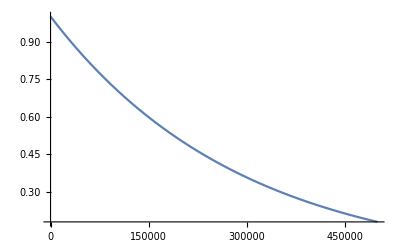

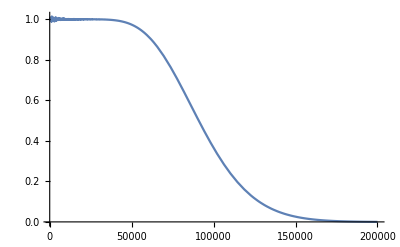

```mathematica
(* Считаем для НЦ *)
(* Сочиняем ручками SurvivalFunction для резервирования с дробной кратностью *)
DiskSurvival[P_,N_, K_]:= ∑_(i=0)^K (Binomial[N+K,i]*(1-P)^i*(P)^(N+K-i))
Subscript[p, 1]=SurvivalFunction[ExponentialDistribution[3425×10^-9],t]; (* 4 Tb *)
Subscript[p, 2]=SurvivalFunction[ExponentialDistribution[3425×10^-9],t];(* 1.2 Tb *)
subdisk1=DiskSurvival[Subscript[p, 1],46,15] //Simplify;
subdisk2=DiskSurvival[Subscript[p, 2],35,12] //Simplify;

Mean[pp] //N;
(* mttf=∫_0^∞ subdisk1 * subdisk2ⅆt //N *)
 mttf=∫_0^∞ subdisk2ⅆt //N 
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)//N (* в годах *)
Plot[Subscript[p, 1],{t,0,500000},PlotRange->All]
Plot[subdisk2,{t,500,200000},PlotRange->All]
```

```mathematica
(* всякие исследования *)
Subscript[z, 1]=SurvivalFunction[ExponentialDistribution[λ],t];
Binomial[50,15]
BooleanCountingFunction[{46,46+15},46+15]@@Array[Subscript[g, #]&,46+15] //BooleanConvert
```